## Introduction

## Main

### Simulations for N >> 1

#### Animation

$Aborted

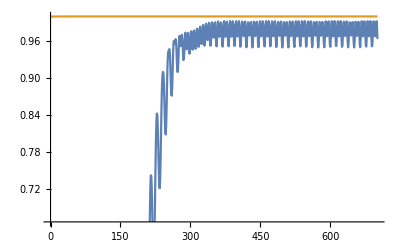

{0.963405,1.}

```mathematica
(*Preamble*)
{dt,n,T}={0.1,100,500}; 
{J,k,b,e}={0.5,0.5,1,5};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,znew}={Table[(2 π j)/n+0.01RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
results=plotResults[znew,pin]
]

ListPlot[{Abs[Wp],Abs[Wm]},Joined->True]

vals={Abs[Wp1],Abs[Wm1]}
```

#### No video

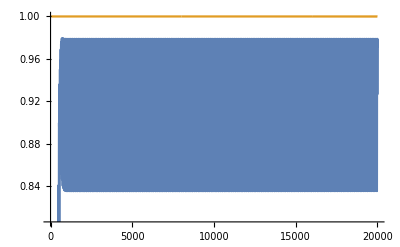

```mathematica
(*Preamble*)
{dt,n,T}={0.05,100,1000}; 
{J,k,b,e}={0.5,0.5,1,3};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,znew}={Table[(2 π j)/n+0.01RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
]
ListPlot[{Abs[Wp],Abs[Wm]},Joined->True]
```

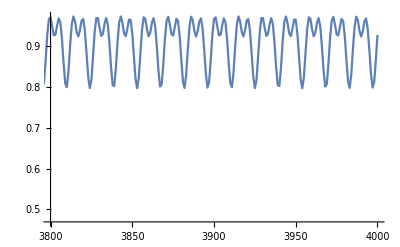

```mathematica
ListPlot[Abs[Wp],Joined->True,PlotRange->{{3800,4000},Automatic}]
```

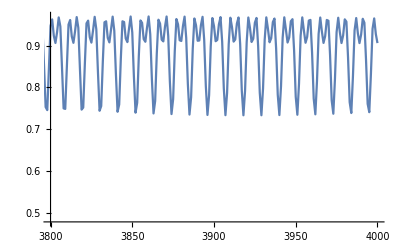

```mathematica
ListPlot[Abs[Wp],Joined->True,PlotRange->{{3800,4000},Automatic}]
```

ListPlot::prng: Value of option PlotRange -> {Automatic} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

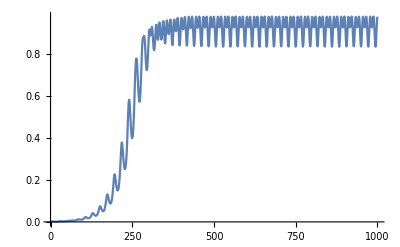

```mathematica
ListPlot[Abs[Wp],Joined->True,PlotRange->{Automatic}]
```

Beautiful! Found chaos

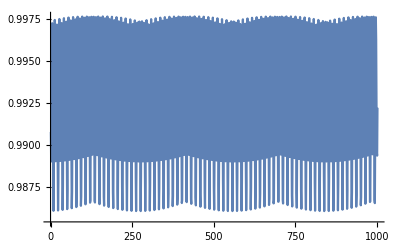

```mathematica
cutoff=Round[0.5*Length[Wp]];
temp=Abs[Wp[[cutoff;;-1]]];
ListPlot[temp,Joined->True]
```

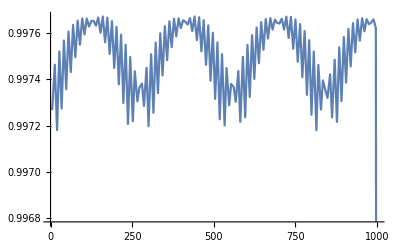

```mathematica
ListPlot[FindPeaks[temp],Joined->True]
```

## Vary E

### Method

```mathematica
run[e_]:=Block[{dt,n,T,J,k,b,Ex,Eθ,b1,b2,z0,znew,z00,pin,Wp,Wm,t,NT,Wp1,Wm1},
(*Preamble*)
{dt,n,T}={0.1,100,2000}; 
{J,k,b}={0.5,0.5,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,znew}={Table[(2 π j)/n+0.01RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
ListPlot[{Abs[Wp],Abs[Wm]},Joined->True,ImageSize->Medium,PlotLabel->"E = "<>ToString[e]]
]
```

### Main

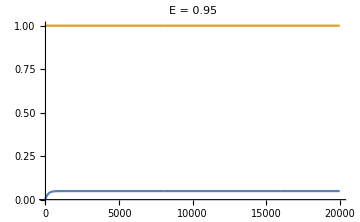

```mathematica
run[0.95]
```

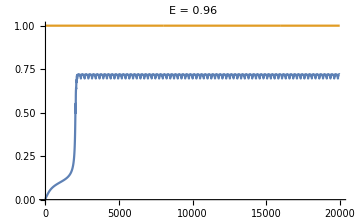

```mathematica
run[0.96]
```

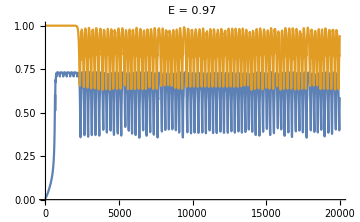

```mathematica
run[0.97]
```

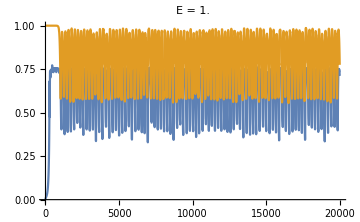

```mathematica
run[1.0]
```

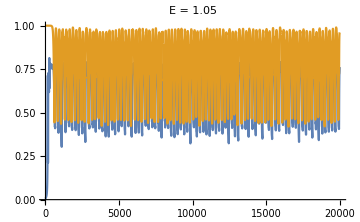

```mathematica
run[1.05]
```

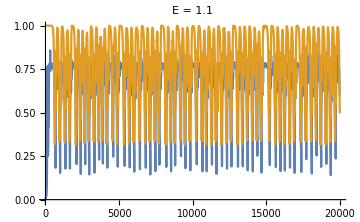

```mathematica
run[1.1]
```

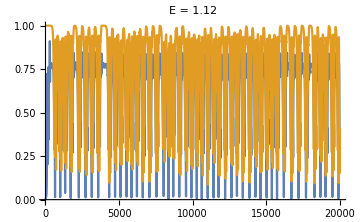

```mathematica
run[1.12]
```

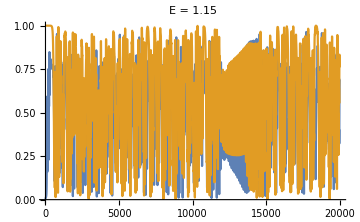

```mathematica
run[1.15]
```

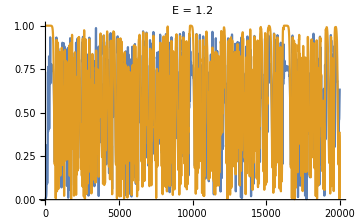

```mathematica
run[1.2]
```

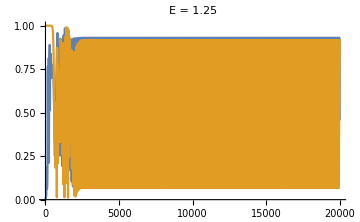

```mathematica
run[1.25]
```

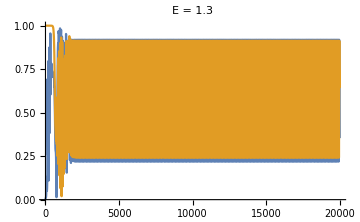

```mathematica
run[1.3]
```

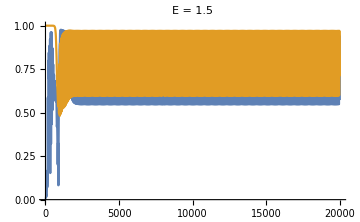

```mathematica
run[1.5]
```

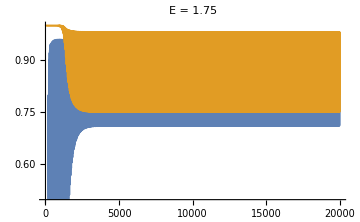

```mathematica
run[1.75]
```

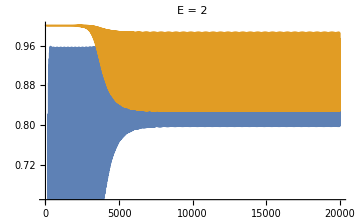

```mathematica
run[2]
```

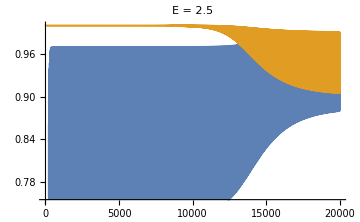

```mathematica
run[2.5]
```

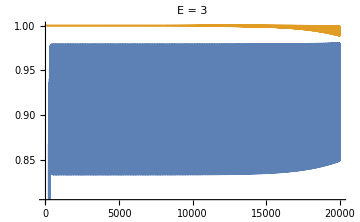

```mathematica
run[3]
```

## Plot in complex plane

```mathematica
run1[e_]:=Block[{dt,n,T,J,k,b,Ex,Eθ,b1,b2,z0,znew,z00,pin,Wp,Wm,t,NT,Wp1,Wm1},
(*Preamble*)
{dt,n,T}={0.1,200,1000}; 
{J,k,b}={0.5,0.5,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,znew}={Table[(2 π j)/n+0.01RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];

cutoff=Round[0.5Length[Wp]];
ListPlot[{Wp[[cutoff;;-1]]//Re,Wp[[cutoff;;-1]]//Im}ᵀ,Joined->True,ImageSize->Medium,PlotLabel->"E = "<>ToString[e],PlotRange->{{-1.1,1.1},{-1.1,1.1}},AxesLabel->{"Re(W_+)","Im(W_+)"},LabelStyle->15]
]
```

### Plot

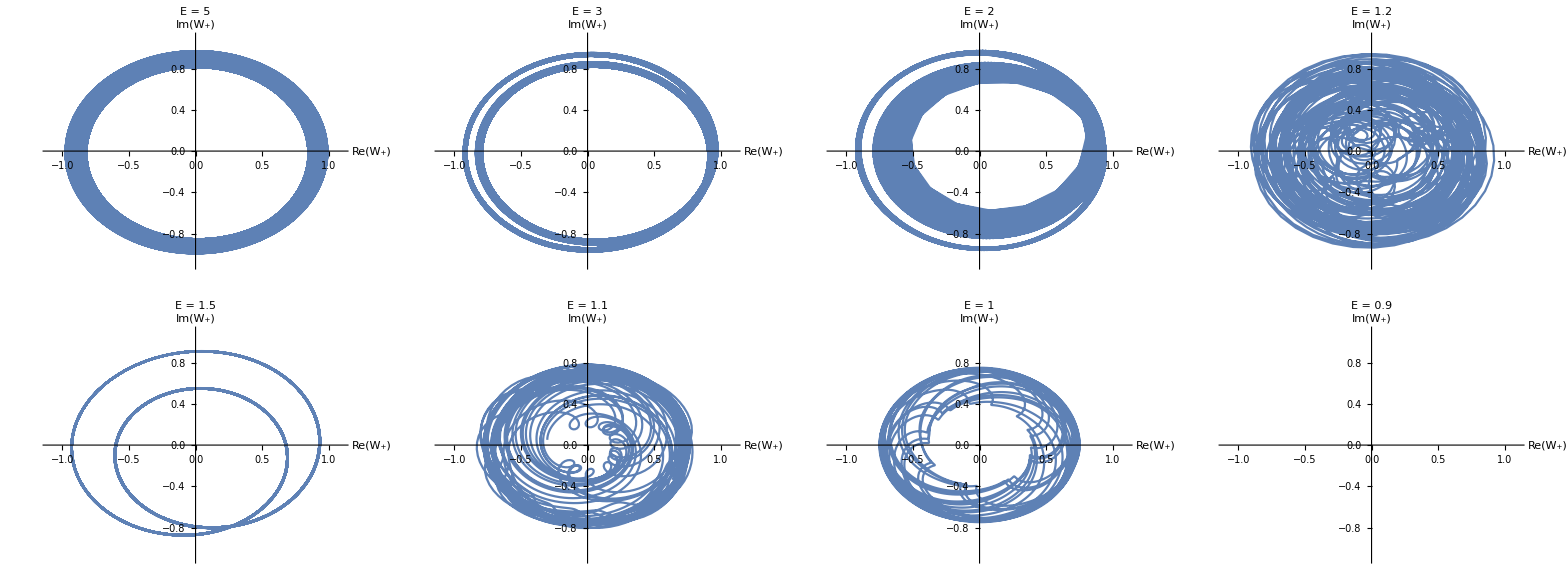

```mathematica
figs=ParallelTable[run1[e],{e,{5,3,2,1.2,1.5,1.1,1,0.9}}];
Grid[Partition[figs,4]]
```

```mathematica
p1=Grid[Partition[figs,4]];
SetDirectory[NotebookDirectory[]];
Export["figures/chaos-j-k-0.5-b-1.png",p1];
```

## Plot (Sp, Sm)

I wonder if there’s a better way to x.

### Method

```mathematica
run2[e_]:=Block[{dt,n,T,J,k,b,Ex,Eθ,b1,b2,z0,znew,z00,t,NT,Wp,Wm,Wp1,Wm1,Sp,Sm,p3},

(*Preamble*)
{dt,n,T}={0.1,200,1000}; 
{J,k,b}={0.5,0.5,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,znew}={Table[(2 π j)/n+0.01RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];

cutoff=Round[0.5*Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]],Abs[Wm[[cutoff;;-1]]]};
p3=ListPlot[{Sp,Sm}ᵀ,PlotRange->{{0,1.1},{0,1.1}},AxesLabel->{"S_+","S_-"},LabelStyle->15,PlotLabel->"E = "<>ToString[e],ImageSize->Medium];
Return[p3]
]
```

### Sim

```mathematica
es={2,1.3,1.25,1.2,1.15,1.1,1,0.9};
figs=ParallelTable[run2[e],{e,es}];
p2=Grid[Partition[figs,4]]
SetDirectory[NotebookDirectory[]];
Export["figure/chaos-Sp-Sm.png",p2]
```

figure/chaos-Sp-Sm.png

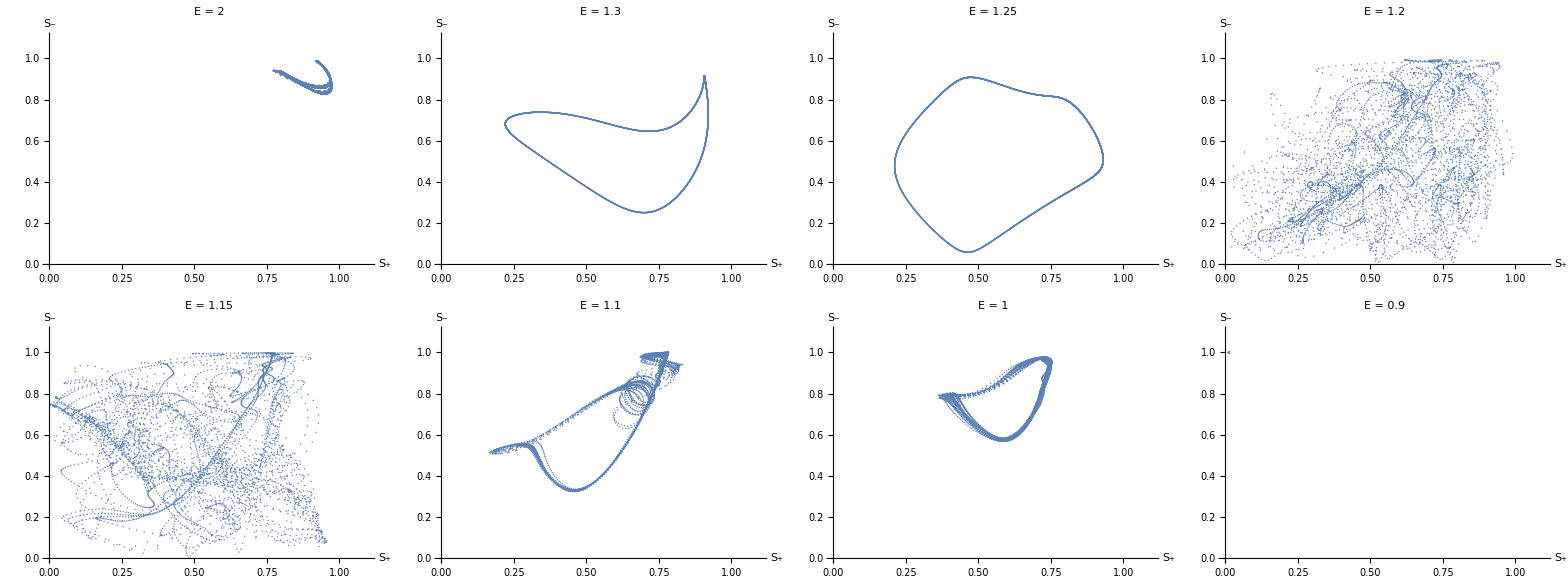

```mathematica
Grid[Partition[figs,4]]
```

#### Zoom in on the period doubling

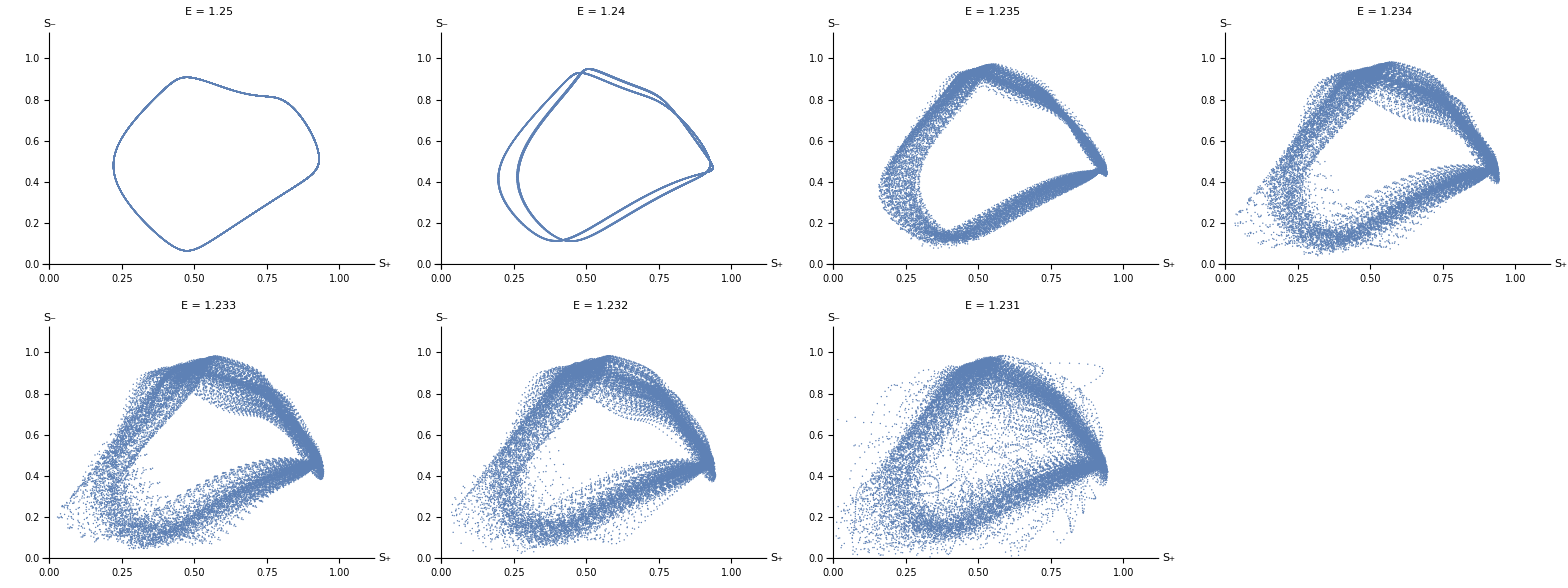

figure/chaos-Sp-Sm-period-doubling.png

```mathematica
run3[e_]:=Block[{dt,n,T,J,k,b,Ex,Eθ,b1,b2,z0,znew,z00,t,NT,Wp,Wm,Wp1,Wm1,Sp,Sm,p3},

(*Preamble*)
{dt,n,T}={0.1,200,5000}; 
{J,k,b}={0.5,0.5,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,znew}={Table[(2 π j)/n+0.01RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];

cutoff=Round[0.5*Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]],Abs[Wm[[cutoff;;-1]]]};
p3=ListPlot[{Sp,Sm}ᵀ,PlotRange->{{0,1.1},{0,1.1}},AxesLabel->{"S_+","S_-"},LabelStyle->15,PlotLabel->"E = "<>ToString[e],ImageSize->Medium];
Return[p3]
]

es={1.25,1.24,1.235,1.234,1.233,1.232,1.231, 1.23};
figs=ParallelTable[run3[e],{e,es}];
p3=Grid[Partition[figs,4]]
SetDirectory[NotebookDirectory[]];
Export["figures/chaos-Sp-Sm-period-doubling.png",p3]
```

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real}, {Ex,_Real}, {Eθ, _Real}, {pin, _Real, 2}, {b1,_Real},{b2,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
vel[[1,i]] = Ex + b1*Sin[pin[[1,i]] - z[[1,i]]];
vel[[2,i]] = Eθ + b2*Sin[pin[[2,i]] - z[[2,i]]];
];
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji]*Cos[thetaji]/N[n];
thetatemp=k*Sin[thetaji]*Cos[xji]/N[n];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
];
vel
(*vel/N[n]*)
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];


eulerStep[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
k2=F[z+dt/2 k1,n,J,k,Ex,Eθ,pin,b1,b2];
k3=F[z+dt/2 k2,n,J,k,Ex,Eθ,pin,b1,b2];
k4=F[z+dt k3,n,J,k,Ex,Eθ,pin,b1,b2];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin,x1,θ1,x2,θ2,ξ1,ξ2,η1,η2,index,n},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
n=Length[x];
index=Round[n/2];
{x1,θ1}={x[[1]],θ[[1]]};
{x2,θ2}={x[[index]],θ[[index]]};
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]},Epilog->{Cyan,PointSize[0.025],Point[{x1,θ1}//mod],Magenta,Point[{x2,θ2}//mod]}];

(*Scatter plot in (ξ,θ) space*)
{ξ1,η1}={x[[1]]+θ[[1]],x[[1]]-θ[[1]]};
{ξ2,η2}={x[[index]]+θ[[index]],x[[index]]-θ[[index]]};
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]},Epilog->{Cyan,PointSize[0.025],Point[{ξ1,η1}//mod],Magenta,Point[{ξ2,η2}//mod]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];
```